```mathematica
Needs["WSMLink`"]
```

```mathematica
hes="rpmgen";
```

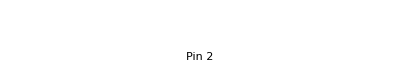
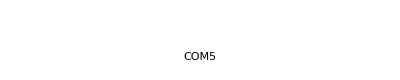
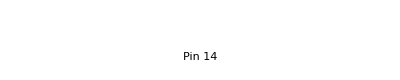
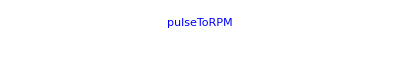
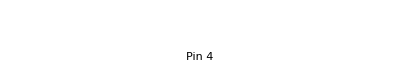
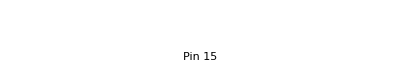
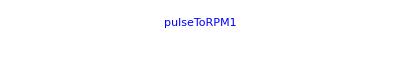
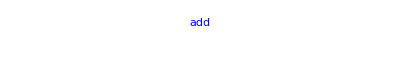
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
WSMModelData[hes,"Diagram"]
```

```mathematica
sim=WSMRealTimeSimulate[hes,500]
```

-Graphics-rpmgen

```mathematica
{WSMRealTimePlot[sim, {"greater.u1"}, 10],WSMRealTimePlot[sim, {"greater1.u1"}, 10]}
```

{,}

```mathematica
u2=Dynamic[{If[sim["greater.u1"]>2.55,1,0],If[sim["greater1.u1"]>2.55,1,0]},UpdateInterval->.0001]
```

```mathematica
rpms=Dynamic[Column[{,sim["pulseToRPM.rpm"],,sim["add.y"],,sim["pulseToRPM.rpm"]-sim["pulseToRPM1.rpm"]}],UpdateInterval->.0001]
```